```mathematica
θ==1/(1+θ)
```

θ==1/(1+θ)

```mathematica
Trace[θ==1/(1+θ)]
```

{{1/(1+θ),1/(1+θ)},θ==1/(1+θ)}

```mathematica
Trace[Solve[θ==1/(1+θ),θ]]
```

{{{1/(1+θ),1/(1+θ)},θ==1/(1+θ)},Solve[θ==1/(1+θ),θ],{{θ→1/2 (-1-√5)},{θ→1/2 (-1+√5)}}}

```mathematica
1/(1+1)
```

1/2

```mathematica
NestList[Function[θ,1/(1+θ)],1,10]
```

{1,1/2,2/3,3/5,5/8,8/13,13/21,21/34,34/55,55/89,89/144}

```mathematica
Map[N,NestList[Function[θ,1/(1+θ)],1,10]]
```

{1.,0.5,0.666667,0.6,0.625,0.615385,0.619048,0.617647,0.618182,0.617978,0.618056}

```mathematica
N[1/2 (-1+√5)]
```

0.618034

```mathematica
Map[#-(1/2 (-1+√5))&,NestList[Function[θ,1/(1+θ)],1,10]]
```

{1+1/2 (1-√5),1/2+1/2 (1-√5),2/3+1/2 (1-√5),3/5+1/2 (1-√5),5/8+1/2 (1-√5),8/13+1/2 (1-√5),13/21+1/2 (1-√5),21/34+1/2 (1-√5),34/55+1/2 (1-√5),55/89+1/2 (1-√5),89/144+1/2 (1-√5)}

```mathematica
Map[N[#-(1/2 (-1+√5))]&,NestList[Function[θ,1/(1+θ)],1,10]]
```

{0.381966,-0.118034,0.0486327,-0.018034,0.00696601,-0.00264937,0.00101363,-0.00038693,0.000147829,-0.0000564607,0.0000215668}

```mathematica
Map[N[Abs[#-(1/2 (-1+√5))]]&,NestList[Function[θ,1/(1+θ)],1,10]]
```

{0.381966,0.118034,0.0486327,0.018034,0.00696601,0.00264937,0.00101363,0.00038693,0.000147829,0.0000564607,0.0000215668}

```mathematica
Map[N[Abs[#-(1/2 (-1+√5))]]&,NestList[Function[θ,1/(1+θ)],1,100]]
```

{0.381966,0.118034,0.0486327,0.018034,0.00696601,0.00264937,0.00101363,0.00038693,0.000147829,0.0000564607,0.0000215668,8.23768×10^-6,3.14653×10^-6,1.20186×10^-6,4.59072×10^-7,1.7535×10^-7,6.69777×10^-8,2.55832×10^-8,9.77191×10^-9,3.73254×10^-9,1.4257×10^-9,5.4457×10^-10,2.08007×10^-10,7.94517×10^-11,3.03478×10^-11,1.15919×10^-11,4.42768×10^-12,1.69131×10^-12,6.45928×10^-13,2.46803×10^-13,9.41469×10^-14,3.60822×10^-14,1.36557×10^-14,5.32907×10^-15,1.9984×10^-15,7.77156×10^-16,2.22045×10^-16,1.11022×10^-16,0.,1.11022×10^-16,0.,1.11022×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.11022×10^-16,0.,-1.11022×10^-16,1.11022×10^-16,-1.11022×10^-16,0.,0.,0.,-1.11022×10^-16,1.11022×10^-16,0.,1.11022×10^-16,0.,1.11022×10^-16,0.,1.11022×10^-16,-1.11022×10^-16,0.,0.,1.11022×10^-16,-1.11022×10^-16,0.,0.}

```mathematica
FunctionExpand[Sin]
```

Sin

```mathematica
FunctionExpand[Sin[x]]
```

Sin[x]

```mathematica
Plot3D[√(1-x^2-y^2),{x,y}∈Disk[]]
```

-Graphics3D-

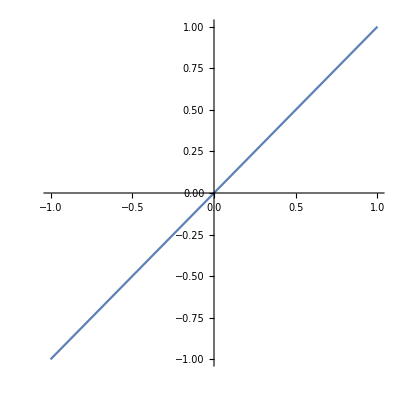

```mathematica
ParametricPlot[
{t,t}
,{t,-1,1}]
```

```mathematica
Show[{
Plot3D[√(1-x^2-y^2),{x,y}∈Disk[]],
ParametricPlot[{t,t},{t,-1,1}]
}]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics3D-,-Graphics-}]

```mathematica
ParametricPlot3D[
{t,t,0}
,{t,-1,1}]
```

-Graphics3D-

```mathematica
Show[{
Plot3D[√(1-x^2-y^2),{x,y}∈Disk[]],
ParametricPlot3D[{t,t,0},{t,-1,1}]
}]
```

-Graphics3D-

```mathematica
Show[{
Plot3D[√(1-x^2-y^2),{x,y}∈Disk[]],
ParametricPlot3D[{t,t,√(1-(t)^2-(t)^2)},{t,-1,1}]
}]
```

-Graphics3D-

```mathematica
Show[{
Plot3D[f[x,y],{x,y}∈Disk[]],
ParametricPlot3D[{x[t],y[t],f[x[t],y[t]]},{t,-1,1}]
}]
```

-Graphics3D-

```mathematica
With[{f=Function[{x,y},√(1-x^2-y^2)],funcx=Function[t,t^2],funcy=Function[t,t(t^2-1)]},
Show[{
Plot3D[f[x,y],{x,y}∈Disk[]],
ParametricPlot3D[{funcx[t],funcy[t],f[funcx[t],funcy[t]]},{t,-1,1}]
}]
]
```

-Graphics3D-

```mathematica
Dt[f[x] g[x]]
```

Dt[x] g[x] f'[x]+Dt[x] f[x] g'[x]

```mathematica
Dt[f[x] g[x]h[x]]
```

Dt[x] g[x] h[x] f'[x]+Dt[x] f[x] h[x] g'[x]+Dt[x] f[x] g[x] h'[x]

```mathematica
Dt[A== length height]
```

Dt[A]==length Dt[height]+height Dt[length]

```mathematica
Dt[Area== length height]
```

Dt[Area]==length Dt[height]+height Dt[length]

```mathematica
TraditionalForm[Dt[Area]==length Dt[height]+height Dt[length]]
```

ⅆArea==length ⅆheight+height ⅆlength

```mathematica
Solve[Dt[Area]==length Dt[height]+height Dt[length],Dt[length]]
```

{{Dt[length]→(Dt[Area]-length Dt[height])/height}}

```mathematica
TraditionalForm[Dt[length]==(Dt[Area]-length Dt[height])/height]
```

ⅆlength==(ⅆArea-length ⅆheight)/height

```mathematica
ComplexPlot[z+1/z,{z,-2-2ⅈ,2+2ⅈ}]
```

-Graphics-

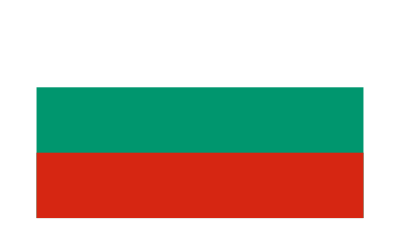

```mathematica
CountryData["Bulgaria","Flag"]
```

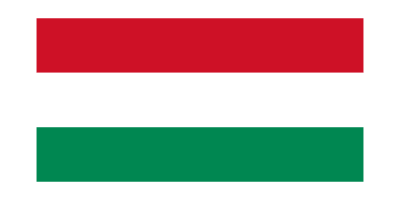

```mathematica
CountryData["Hungary","Flag"]
```

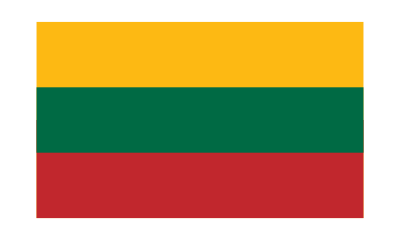

```mathematica
CountryData["Lithuania","Flag"]
```

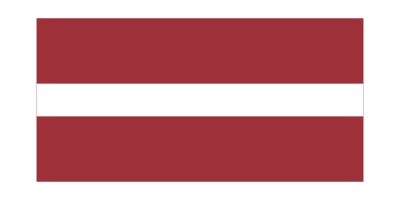

```mathematica
CountryData["Latvia","Flag"]
```

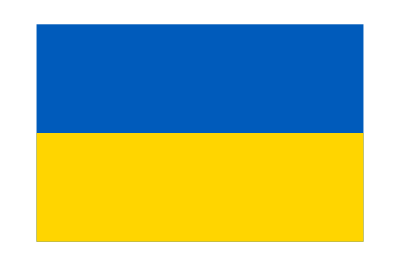

```mathematica
CountryData["Ukraine","Flag"]
```

```mathematica
CountryData["Europe"]
```

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

```mathematica
Grid@
ReverseSortBy[
Map[Function[country,
{country,CountryData[country,"GDPPerCapita"]}]
,CountryData["Europe"]]
,Last]
```

Liechtenstein | 168146. $
Monaco | 163352. $
Luxembourg | 102831. $
Isle of Man | 81672. $
Switzerland | 78812.7 $
Norway | 70812.5 $
Ireland | 61606.5 $
Iceland | 59976.9 $
Jersey | 57000. $
Faroe Islands | 54117.8 $
Denmark | 53417.7 $
Sweden | 51599.9 $
San Marino | 47908.6 $
Netherlands | 45294.8 $
Guernsey | 44600. $
Austria | 44176.5 $
Finland | 43090.2 $
Germany | 41936.1 $
Belgium | 41096.2 $
United Kingdom | 39899.4 $
Gibraltar | 38200. $
Andorra | 36988.6 $
France | 36855. $
Italy | 30527.3 $
Spain | 26528.5 $
Malta | 25058.2 $
Cyprus | 23324.2 $
Slovenia | 21304.6 $
Portugal | 19813.3 $
Czech Republic | 18266.5 $
Greece | 18104. $
Estonia | 17574.7 $
Slovakia | 16496. $
Lithuania | 14879.7 $
Latvia | 14118.1 $
Hungary | 12664.8 $
Poland | 12372.4 $
Croatia | 12090.7 $
Romania | 9474.13 $
Bulgaria | 7350.8 $
Montenegro | 6701. $
Serbia | 5348.29 $
Macedonia | 5237.15 $
Belarus | 4989.25 $
Bosnia and Herzegovina | 4708.72 $
Albania | 4146.9 $
Kosovo | 3661.43 $
Ukraine | 2185.73 $
Moldova | 1843.24 $
Vatican City | Missing[NotAvailable]
Svalbard | Missing[NotAvailable]

```mathematica
Grid@
ReverseSortBy[
Map[Function[country,
{country,CountryData[country,"GDPPerCapita"]}
],CountryData["Europe"]]
,Last]
```

Liechtenstein | 168146. $
Monaco | 163352. $
Luxembourg | 102831. $
Isle of Man | 81672. $
Switzerland | 78812.7 $
Norway | 70812.5 $
Ireland | 61606.5 $
Iceland | 59976.9 $
Jersey | 57000. $
Faroe Islands | 54117.8 $
Denmark | 53417.7 $
Sweden | 51599.9 $
San Marino | 47908.6 $
Netherlands | 45294.8 $
Guernsey | 44600. $
Austria | 44176.5 $
Finland | 43090.2 $
Germany | 41936.1 $
Belgium | 41096.2 $
United Kingdom | 39899.4 $
Gibraltar | 38200. $
Andorra | 36988.6 $
France | 36855. $
Italy | 30527.3 $
Spain | 26528.5 $
Malta | 25058.2 $
Cyprus | 23324.2 $
Slovenia | 21304.6 $
Portugal | 19813.3 $
Czech Republic | 18266.5 $
Greece | 18104. $
Estonia | 17574.7 $
Slovakia | 16496. $
Lithuania | 14879.7 $
Latvia | 14118.1 $
Hungary | 12664.8 $
Poland | 12372.4 $
Croatia | 12090.7 $
Romania | 9474.13 $
Bulgaria | 7350.8 $
Montenegro | 6701. $
Serbia | 5348.29 $
Macedonia | 5237.15 $
Belarus | 4989.25 $
Bosnia and Herzegovina | 4708.72 $
Albania | 4146.9 $
Kosovo | 3661.43 $
Ukraine | 2185.73 $
Moldova | 1843.24 $
Vatican City | Missing[NotAvailable]
Svalbard | Missing[NotAvailable]

```mathematica
Map[Function[country,
{country,CountryData[country,"GDPPerCapita"]}
],
Select[CountryData["Europe"],Not@MissingQ@CountryData[#,"GDPPerCapita"]&]]
```

{{Albania,4146.9 $},{Andorra,36988.6 $},{Austria,44176.5 $},{Belarus,4989.25 $},{Belgium,41096.2 $},{Bosnia and Herzegovina,4708.72 $},{Bulgaria,7350.8 $},{Croatia,12090.7 $},{Cyprus,23324.2 $},{Czech Republic,18266.5 $},{Denmark,53417.7 $},{Estonia,17574.7 $},{Faroe Islands,54117.8 $},{Finland,43090.2 $},{France,36855. $},{Germany,41936.1 $},{Gibraltar,38200. $},{Greece,18104. $},{Guernsey,44600. $},{Hungary,12664.8 $},{Iceland,59976.9 $},{Ireland,61606.5 $},{Isle of Man,81672. $},{Italy,30527.3 $},{Jersey,57000. $},{Kosovo,3661.43 $},{Latvia,14118.1 $},{Liechtenstein,168146. $},{Lithuania,14879.7 $},{Luxembourg,102831. $},{Macedonia,5237.15 $},{Malta,25058.2 $},{Moldova,1843.24 $},{Monaco,163352. $},{Montenegro,6701. $},{Netherlands,45294.8 $},{Norway,70812.5 $},{Poland,12372.4 $},{Portugal,19813.3 $},{Romania,9474.13 $},{San Marino,47908.6 $},{Serbia,5348.29 $},{Slovakia,16496. $},{Slovenia,21304.6 $},{Spain,26528.5 $},{Sweden,51599.9 $},{Switzerland,78812.7 $},{Ukraine,2185.73 $},{United Kingdom,39899.4 $}}

```mathematica
Map[Function[country,
QuantityMagnitude@CountryData[country,"GDPPerCapita"]
],
Select[CountryData["Europe"],Not@MissingQ@CountryData[#,"GDPPerCapita"]&]]
```

{4146.9,36988.6,44176.5,4989.25,41096.2,4708.72,7350.8,12090.7,23324.2,18266.5,53417.7,17574.7,54117.8,43090.2,36855.,41936.1,38200.,18104.,44600.,12664.8,59976.9,61606.5,81672.,30527.3,57000.,3661.43,14118.1,168146.,14879.7,102831.,5237.15,25058.2,1843.24,163352.,6701.,45294.8,70812.5,12372.4,19813.3,9474.13,47908.6,5348.29,16496.,21304.6,26528.5,51599.9,78812.7,2185.73,39899.4}

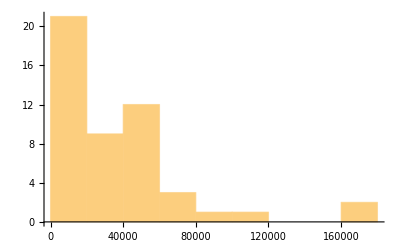

```mathematica
Histogram[%40]
```

```mathematica
Sort[%40]
```

{1843.24,2185.73,3661.43,4146.9,4708.72,4989.25,5237.15,5348.29,6701.,7350.8,9474.13,12090.7,12372.4,12664.8,14118.1,14879.7,16496.,17574.7,18104.,18266.5,19813.3,21304.6,23324.2,25058.2,26528.5,30527.3,36855.,36988.6,38200.,39899.4,41096.2,41936.1,43090.2,44176.5,44600.,45294.8,47908.6,51599.9,53417.7,54117.8,57000.,59976.9,61606.5,70812.5,78812.7,81672.,102831.,163352.,168146.}

```mathematica
Dt[F=m a]
```

m Dt[a]+a Dt[m]

```mathematica
Information[F]
```

Information[a m]

```mathematica
ClearAll[F]
```

```mathematica
Dt[F==m a]
```

Dt[F]==m Dt[a]+a Dt[m]

```mathematica
Dt[F==m a[t]]
```

Dt[F]==a[t] Dt[m]+m Dt[t] a'[t]

```mathematica
Solve[Dt[F]==a[t] Dt[m]+m Dt[t] a'[t],a'[t]]
```

{{a'[t]→(Dt[F]-a[t] Dt[m])/(m Dt[t])}}

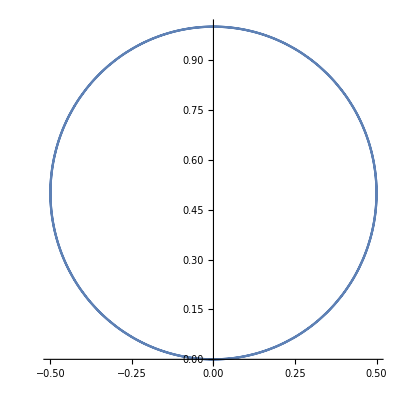

```mathematica
ParametricPlot[
{Sin[t]Cos[t],Sin[t]Sin[t]}
,{t,0,2π}]
```

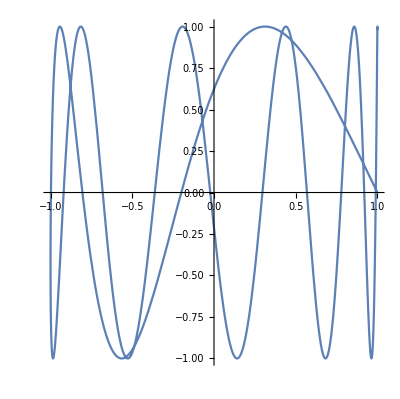

```mathematica
ParametricPlot[
{Cos[t],Sin[t^2]}
,{t,0,2π}]
```

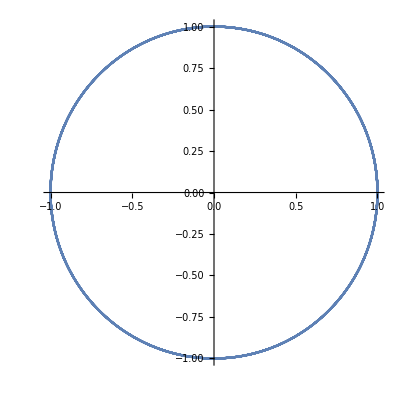

```mathematica
ParametricPlot[
{Cos[t^2],Sin[t^2]}
,{t,0,2π}]
```

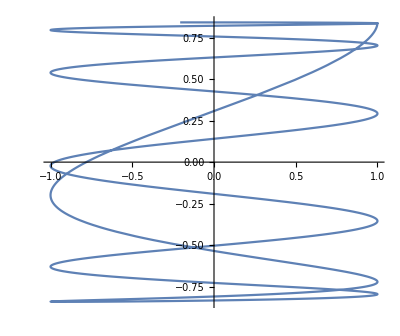

```mathematica
ParametricPlot[
{Cos[t^2],Sin[Cos[t]]}
,{t,0,2π}]
```

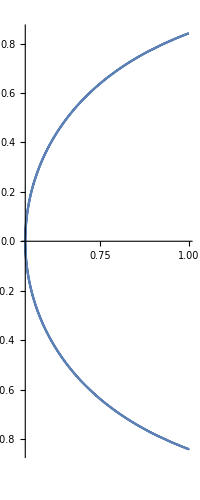

```mathematica
ParametricPlot[
{Cos[Sin[t]],Sin[Cos[t]]}
,{t,0,2π}]
```

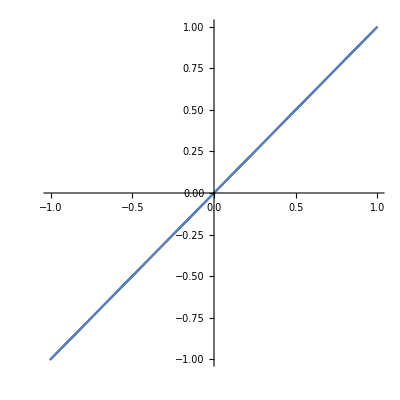

```mathematica
ParametricPlot[
{Cos[t],Cos[t]}
,{t,0,2π}]
```



```mathematica
ParametricPlot[
{Cos[t],Sin[t]}
,{t,0,2π}]
```

```mathematica
D[{Cos[t],Sin[t]},t]
```

{-Sin[t],Cos[t]}

```mathematica
J[{a_,b_}]:={-b,a}
```

```mathematica
J@D[{Cos[t],Sin[t]},t]
```

{-Cos[t],-Sin[t]}

```mathematica
{-Cos[t],-Sin[t]}
```

```mathematica
Manipulate[
ParametricPlot[{
{Cos[t],Sin[t]},
{Cos[a]t,Sin[a]t}
},{t,0,2π}]
,{a,0,2π}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot[{
{Cos[t],Sin[t]},
{Cos[a]t,Sin[a]t}
},{t,0,2π}],
ListPlot[{{Cos[a],Sin[a]}}]
}],{a,0,2π}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot[{
{Cos[t],Sin[t]},
{Cos[a]t,Sin[a]t}
},{t,0,2π},PlotRange->{{-1,1},{-1,1}}],
ListPlot[{{Cos[a],Sin[a]}}]
}],{a,0,2π}]
```

```mathematica
FullSimplify[Norm[{Cos[t],Sin[t]}]==1+Sin[t],t∈Reals∧0≤t≤2π]
```

Sin[t]==0

```mathematica
FullSimplify[Norm[{x[t],y[t]}]==1+Sin[t],t∈Reals∧0≤t≤2π]
```

√(Abs[x[t]]^2+Abs[y[t]]^2)==1+Sin[t]

```mathematica
FullSimplify[Norm[{x[t],y[t]}]==1+Sin[t],{t,x[t],y[t]}∈Reals∧0≤t≤2π]
```

√(x[t]^2+y[t]^2)==1+Sin[t]

```mathematica
Reduce[√(x[t]^2+y[t]^2)==1+Sin[t]]
```

Sin[t]==-1+√(x[t]^2+y[t]^2)

```mathematica
Solve[√(x[t]^2+y[t]^2)==1+Sin[t],x[t]]
```

{{x[t]→-√(1+2 Sin[t]+Sin[t]^2-y[t]^2)},{x[t]→√(1+2 Sin[t]+Sin[t]^2-y[t]^2)}}

```mathematica
Solve[√(x[t]^2+y[t]^2)==1+Sin[t],y[t]]
```

{{y[t]→-√(1+2 Sin[t]+Sin[t]^2-x[t]^2)},{y[t]→√(1+2 Sin[t]+Sin[t]^2-x[t]^2)}}

```mathematica
Solve[{√(x[t]^2+y[t]^2)==1+Sin[t],x[t]==Cos[t]},{x[t],y[t]}]
```

{{x[t]→Cos[t],y[t]→-√(1-Cos[t]^2+2 Sin[t]+Sin[t]^2)},{x[t]→Cos[t],y[t]→√(1-Cos[t]^2+2 Sin[t]+Sin[t]^2)}}

```mathematica
Last[%%]
```

{y[t]→√(1+2 Sin[t]+Sin[t]^2-x[t]^2)}

```mathematica
{Cos[t],√(1-Cos[t]^2+2 Sin[t]+Sin[t]^2)}
```

```mathematica
Cos[t],y[t]->√(1-Cos[t]^2+2 Sin[t]+Sin[t]^2)
```

```mathematica
Manipulate[
Show[{
ParametricPlot[{
{Cos[t],Sin[t]},
{Cos[a]t,Sin[a]t},
{Cos[t],√(1-Cos[t]^2+2 Sin[t]+Sin[t]^2)}
},{t,0,2π},PlotRange->{{-1,1},{-1,1}}],
ListPlot[{{Cos[a],Sin[a]}}]
}],{a,0,2π}]
```

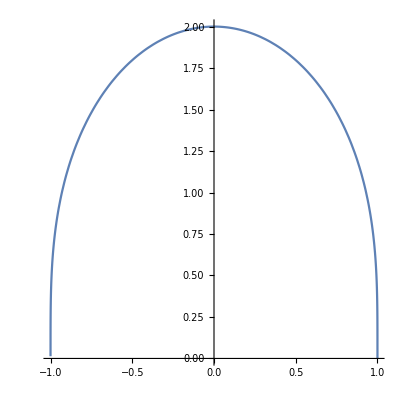

```mathematica
ParametricPlot[
{Cos[t],√(1-Cos[t]^2+2 Sin[t]+Sin[t]^2)}
,{t,0,2π}]
```

```mathematica
PolarPlot[1,{θ,0,2π}]
```

-Graphics-

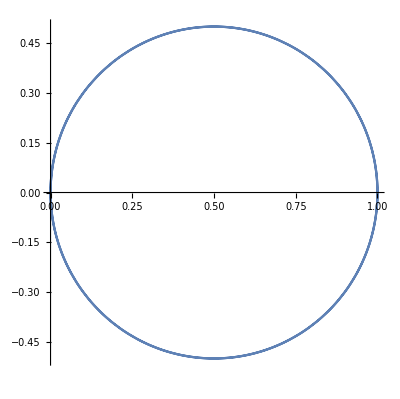

```mathematica
PolarPlot[Cos[θ],{θ,0,2π}]
```

```mathematica
PolarPlot[1,{θ,0,2π}]
```

```mathematica
NBodySimulation["Harmonic",{<|"Mass"->1,"Position"->{-1/3},"Velocity"->{0}|>,
<|"Mass"->2,"Position"->{1/3},"Velocity"->{0}|>},10]
```

NBodySimulationData[…]

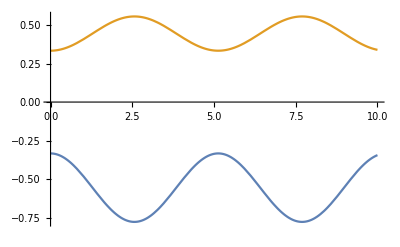

```mathematica
Plot[Evaluate[Out[78][All,"Position",t]],{t,0,10}]
```

```mathematica
NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,.5}|>,
<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,-.5}|>,
<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>},4]
```

NBodySimulationData[3, <4.>]

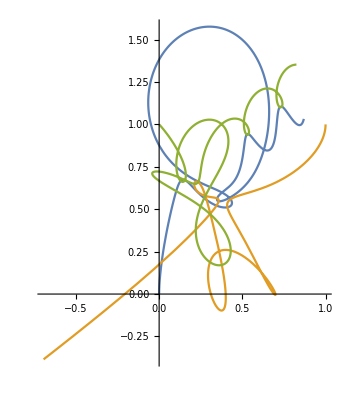

```mathematica
ParametricPlot[Evaluate[Out[80][All,"Position",t]],{t,0,4}]
```

```mathematica
Manipulate[
ParametricPlot[
Evaluate[Out[80][All,"Position",t]],{t,0,α}]
,{α,0,4}]
```

ParametricPlot::plld: Endpoints for t in {t,0,FE`α$$292} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

```mathematica
NBodySimulation["InverseSquare",{<|"Mass"->10,"Position"->{0,0},"Velocity"->{0,.5}|>,
<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,-.5}|>,
<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>},4]
```

NBodySimulationData[3, <4.>]

```mathematica
Manipulate[
ParametricPlot[
Evaluate[Out[83][All,"Position",t]],{t,0,α}]
,{α,0,4}]
```

ParametricPlot::plld: Endpoints for t in {t,0,FE`α$$304} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

ParametricPlot::plld: Endpoints for t in {t,0,FE`α$$304} must have distinct machine-precision numerical values.

```mathematica
a∧b==c
```

a&&b==c

```mathematica
a∧b->a
```

a&&b→a

```mathematica
(¬a∨a)∧b==c
```

(!a||a)&&b==c

```mathematica
(¬a∨a)∧b==¬a∨c
```

((!a||a)&&b==!a)||c

```mathematica
Reduce[(¬a∨a)∧b->¬a∨c]
```

Reduce::naqs: (!a||a)&&b→!a||c is not a quantified system of equations and inequalities.

Reduce[(!a||a)&&b→!a||c]

```mathematica
b->¬a∨c
```

b→!a||c

```mathematica
a->b->c->d
```

a→b→c→d

```mathematica
a(b+c)==a b+ a c
```

a (b+c)==a b+a c

```mathematica
Reduce[a (b+c)==a b+a c]
```

True

```mathematica
a∧(b∨c)==a∧b∨a∧c
```

(a&&(b||c)==a&&b)||(a&&c)